```mathematica
$Assumptions={k ∈ Integers,n ∈ Integers,Ν∈Integers}
2-1/h^2((Sin[(π (2k+1)(n+1))/(2Ν-1)]-2 Sin[(π (2k+1)n)/(2Ν-1)]+Sin[(π (2k+1)(n-1))/(2Ν-1)])/Sin[(π (2k+1)n)/(2Ν-1)])//FullSimplify
```

{k∈ℤ,n∈ℤ,Ν∈ℤ}

(2 (1+h^2-Cos[(π+2 k π)/(1-2 Ν)]))/h^2

```mathematica
2-ⅇ^((π k ⅈ)/(Ν-1))-ⅇ^(-(π k ⅈ)/(Ν-1))//FullSimplify
```

2-2 Cos[(k π)/(-1+Ν)]

```mathematica
(13 q^5+(13+α)q^4+(α+7)q^3 +(α+7)q^2+(α+1)q+1)/(1+q)//Simplify
```

```mathematica
1+7 q^2+13 q^4+q α+q^3 α //TeXForm
```

\alpha  q^3+13 q^4+7 q^2+\alpha  q+1

```mathematica
f[z_,0]:=1+7 z^2+13 z^4+z α+z^3 α
```

```mathematica
f[z_,n_]:=1/z(Last[CoefficientList[f[z,n-1],z]]f[z,n-1]-First[CoefficientList[f[z,n-1],z]] z^Exponent[f[z,n-1],z] f[1/z,n-1])//Simplify
```

```mathematica
f[z,4]
```

4129544208384 (86436-1225 α^2+4 α^4)

```mathematica
Reduce[RealAbs[2 (-147+α^2)]>RealAbs[-7α],α]
```

α<-14||-21/2<α<21/2||α>14

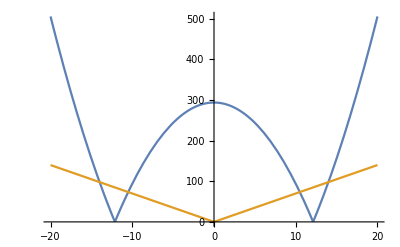

```mathematica
Plot[{RealAbs[2 (-147+α^2)],RealAbs[-7α]},{α,-20,20}]
```

```mathematica
1+7 q^2+13 q^4+q α+q^3 α /.α->-21/2//FullSimplify
```

1/2 (-1+q) (-2+q (19+q (5+26 q)))

```mathematica
1-13 q-7 q^2-7 q^3-q^4+13 q^5//FullSimplify
```

(1+q) (1+q (-14+q (7+q (-14+13 q))))

```mathematica
1+7 z^2+13 z^4+z α+z^3 α//TeXForm
```

\alpha  z^3+13 z^4+7 z^2+\alpha  z+1

```mathematica
-2+q (19+q (5+26 q))
```

```mathematica
-2+q (19+q (5+26 q))//Expand//TeXForm
```

26 q^3+5 q^2+19 q-2

```mathematica
A=({{1-q, -1}, {-2, -q}})
```

{{1-q,-1},{-2,-q}}

```mathematica
Solve[Det[A]==0,q]
```

{{q→-1},{q→2}}

```mathematica
Eigensystem[A]
```

{{7,-1},{{1,3},{3,1}}}

```mathematica
A=({{-2, 3}, {-3, 8}})
```

{{-2,3},{-3,8}}

```mathematica
Solve[{4a==3b+5,-6b+3a==30,3c==3d-6,-7d+3c+2==0},{a,b,c,d}]
```

{{a→-4,b→-7,c→-3,d→-1}}

```mathematica
A= ({{1000(1-Subscript[y, 1]^2), 1}, {-1, 0}})
```

{{1000 (1-y_1^2),1},{-1,0}}

```mathematica
Eigenvalues[A]//FullSimplify
```

{1/2 (1000-1000 y_1^2-√(-4+1000000 (-1+y_1^2)^2)),1/2 (1000-1000 y_1^2+√(-4+1000000 (-1+y_1^2)^2))}

```mathematica
$Assumptions={λ≥0,Λ≥0,Subscript[y, 1]∈Reals}
Reduce[{Re[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]≤ -Λ,
RealAbs[Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]]≤Λ,
Abs[1/2 (1000-1000 Subscript[y, 1]^2+√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]≤λ},Subscript[y, 1]]
```

{λ≥0,Λ≥0,y_1∈ℝ}

```mathematica
Plot
```

Plot

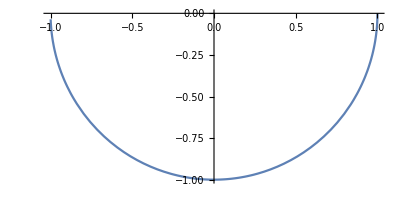

```mathematica
ParametricPlot[{Re[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))],Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]},{Subscript[y, 1],-(√(501/5))/10,-(√(499/5))/10}]
```

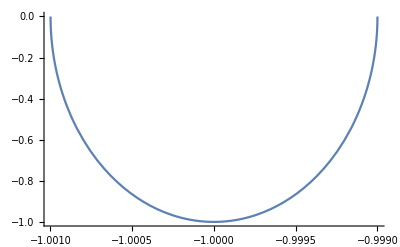

```mathematica
Plot[Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))],{Subscript[y, 1],-(√(501/5))/10,-(√(499/5))/10}]
```

```mathematica
Reduce[-4+1000000 (-1+Subscript[y, 1]^2)^2≤0,Subscript[y, 1]]//FullSimplify
```

-(√(501/5))/10≤y_1≤-(√(499/5))/10||(√(499/5))/10≤y_1≤(√(501/5))/10

```mathematica
Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]
```

1/2 Im[-1000 y_1^2-√(-4+1000000 (-1+y_1^2)^2)]

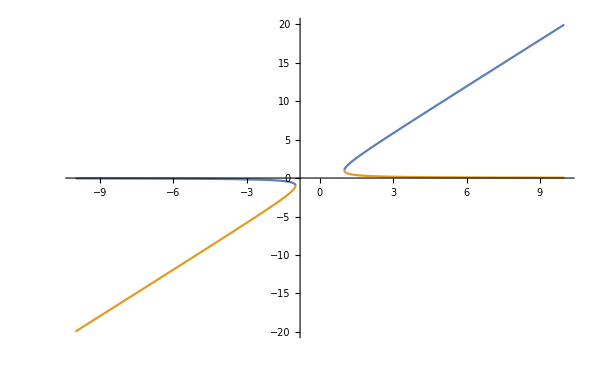

```mathematica
Show[Plot[{x+√(x^2-1),x-√(x^2-1)},{x,-10,-1},PlotRange->All],Plot[{x+√(x^2-1),x-√(x^2-1)},{x,1,10}]]
```

```mathematica
$Assumptions={x≤ -1}
```

{x≤-1}

```mathematica
(x-√(x^2-1))/(x+√(x^2-1))//FullSimplify
```

-1+2 x (x-√(-1+x^2))

```mathematica
-1+2 x (x-√(-1+x^2))/.x->500(1-Subscript[y, 1]^2)//FullSimplify//TeXForm
```

1000 \left(1-y_1^2\right) \left(-500 \left(y_1^2-1\right)-\sqrt{250000
   \left(y_1^2-1\right){}^2-1}\right)-1

```mathematica
Reduce[RealAbs[-1+1000 (1-Subscript[y, 1]^2) (500 (1-Subscript[y, 1]^2)-√(-1+250000 (1-Subscript[y, 1]^2)^2))]≤1/10,Subscript[y, 1]]//FullSimplify
```

-1/100 √(10000-11 √10)≤y_1≤1/100 √(10000-11 √10)

```mathematica
-1+2 x (x-√(-1+x^2))//TeXForm
```

2 x \left(x-\sqrt{x^2-1}\right)-1

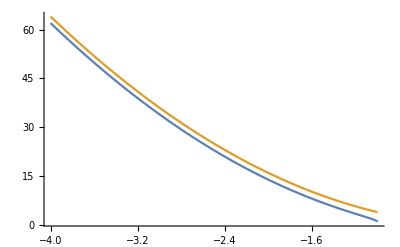

```mathematica
Plot[{(x-√(x^2-1))/(x+√(x^2-1)),4 x^2},{x,-4,-1},PlotRange->All]
```

```mathematica
Series[-1+2 x (x-√(-1+x^2)),x->-∞]//Normal//FullSimplify
```

4 x^2

```mathematica
-1+2 x (x-√(-1+x^2))//TeXForm
```

2 x \left(x-\sqrt{x^2-1}\right)-1

```mathematica
4 x^2/. x->500(1-Subscript[y, 1]^2)
```

1000000 (1-y_1^2)^2

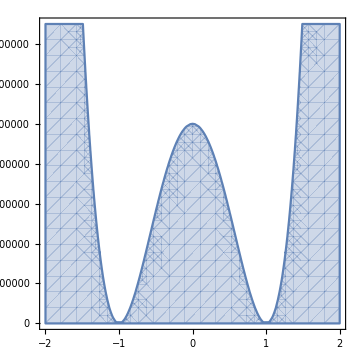

```mathematica
RegionPlot[1000000 (1-Subscript[y, 1]^2)^2≥α,{Subscript[y, 1],-2,2},{α,0,1.5 10^6},ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif"},FrameLabel->MaTeX@{"y_1","\\alpha"},LabelStyle->{NumberPoint->","}]
```

```mathematica
$Assumptions={α>0}
```

{α>0}

```mathematica
Reduce[1000000 (1-Subscript[y, 1]^2)^2≥α,Subscript[y, 1]]
```

y_1∈ℝ&&(α≤0||(0<α<1000000&&(y_1≤-√(1+(√α)/1000)||-√(1-(√α)/1000)≤y_1≤√(1-(√α)/1000)||y_1≥√(1+(√α)/1000)))||(α==1000000&&(y_1≤-√2||y_1==0||y_1≥√2))||(α>1000000&&(y_1≤-√(1+(√α)/1000)||y_1≥√(1+(√α)/1000))))

```mathematica
<<MaTeX`
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathtext}" ,
"\\usepackage[T2A]{fontenc}",
"\\usepackage[utf8]{inputenc}",
"\\usepackage[english,russian]{babel}",
"\\usepackage{units}"}];
```

```mathematica
1000000 (1-Subscript[y, 1]^2)^2≥α//TeXForm
```

1000000 \left(1-y_1^2\right){}^2\geq \alpha

```mathematica
Series[u[Subscript[x, n]+h],{h,0,4}]//Normal/.{u[Subscript[x, n]]-> Subscript[u, n],u'[Subscript[x, n]]->f[Subscript[x, n],Subscript[u, n]],u''[Subscript[x, n]]-> D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}/.x->Subscript[x, n]
```

u_n[x_n]+h u_n'[x_n]+1/2 h^2 u_n''[x_n]+1/6 h^3 u_n^(3)[x_n]+1/24 h^4 u_n^(4)[x_n]

```mathematica
Series[u[Subscript[x, n]+h],{h,0,4}]//Normal
```

u[x_n]+h u'[x_n]+1/2 h^2 u''[x_n]+1/6 h^3 u^(3)[x_n]+1/24 h^4 u^(4)[x_n]

```mathematica
Subscript[u, n][Subscript[x, n]]+h Subscript[u, n]'[Subscript[x, n]]+1/2 h^2 Subscript[u, n]''[Subscript[x, n]]+1/6 h^3 Derivative[3][Subscript[u, n]][Subscript[x, n]]+1/24 h^4 Derivative[4][Subscript[u, n]][Subscript[x, n]]/. Derivative[i_][Subscript[u, n]][_]:>   Derivative[i-1][f][x]
```

```mathematica
h f[x]+Subscript[u, n][Subscript[x, n]]+1/2 h^2 f'[x]+1/6 h^3 f''[x]+1/24 h^4 Derivative[3][f][x,]
```

```mathematica
CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h]
```

{u_n,f[x_n,u_n],1/2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]),1/6 (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]),1/24 ((f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]+2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])+f[x_n,u_n] f^(2,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])+f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])+f^(3,0)[x_n,u_n])}

```mathematica
Normal[Series[u[x+h],{h,0,4}]](*/.u'[x]->f[x,u[x]]*)
```

u[x]+h u'[x]+1/2 h^2 u''[x]+1/6 h^3 u^(3)[x]+1/24 h^4 u^(4)[x]

```mathematica
h f[x,u[x]]+u[x]+1/2 h^2 f'[x,u[x]]+1/6 h^3 f''[x,u[x]]+1/24 h^4 Derivative[3][f][x,u[x]] //Evaluate
```

h f[x,u[x]]+u[x]+1/2 h^2 f'[x,u[x]]+1/6 h^3 f''[x,u[x]]+1/24 h^4 f^(3)[x,u[x]]

```mathematica
FullForm[Series[u[Subscript[x, n]+h],{h,0,4}]//Normal]
```

Plus[u[Subscript[x,n]],Times[h,Derivative[1][u][Subscript[x,n]]],Times[Rational[1,2],Power[h,2],Derivative[2][u][Subscript[x,n]]],Times[Rational[1,6],Power[h,3],Derivative[3][u][Subscript[x,n]]],Times[Rational[1,24],Power[h,4],Derivative[4][u][Subscript[x,n]]]]

```mathematica
FullForm[Series[u[Subscript[x, n]+h],{h,0,4}]//Normal]
```

Plus[u[Subscript[x,n]],Times[h,Derivative[1][u][Subscript[x,n]]],Times[Rational[1,2],Power[h,2],Derivative[2][u][Subscript[x,n]]],Times[Rational[1,6],Power[h,3],Derivative[3][u][Subscript[x,n]]],Times[Rational[1,24],Power[h,4],Derivative[4][u][Subscript[x,n]]]]

```mathematica
Unevaluated[D[f[x,u[x]], x]] //FullForm
```

Unevaluated[D[f[x,u[x]],x]]

```mathematica
D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}/.x->Subscript[x, n]
```

f[x_n,u[x_n]] f^(0,1)[x_n,u[x_n]]+f^(1,0)[x_n,u[x_n]]

```mathematica
D[f[x,u[x]], {x,2}]/.{u'[x]->f[x,u[x]],u''[x]->{D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}}}
```

{f^(0,1)[x,u[x]] (f[x,u[x]] f^(0,1)[x,u[x]]+f^(1,0)[x,u[x]])+f[x,u[x]] f^(1,1)[x,u[x]]+f[x,u[x]] (f[x,u[x]] f^(0,2)[x,u[x]]+f^(1,1)[x,u[x]])+f^(2,0)[x,u[x]]}

```mathematica
s=2;
Subscript[k, i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
Subscript[y, n+1]=Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] Subscript[k, i]
```

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]], h]/.h->0
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]], {h,2}]/.h->0
```

(2 a_(i,1) k_1'[0]+2 a_(i,2) k_2'[0]) f^(0,1)[x_n,y_n]+(a_(i,1) k_1[0]+a_(i,2) k_2[0]) ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,2)[x_n,y_n]+c_i f^(1,1)[x_n,y_n])+c_i ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(1,1)[x_n,y_n]+c_i f^(2,0)[x_n,y_n])

```mathematica
Subscript[y, i]=.
```

```mathematica
f[Subscript[x, n]+Subscript[c, i] h ϵ,Subscript[y, n]+h ϵ ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
```

```mathematica
s=2;
CoefficientList[Subscript[y, n]+h∑_(i=1)^s (Subscript[b, i] Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1})//FullSimplify,h]
```

{y_n,f[x_n,y_n] (b_1+b_2),(b_1 (k_1 a_(1,1)+k_2 a_(1,2))+b_2 (k_1 a_(2,1)+k_2 a_(2,2))) f^(0,1)[x_n,y_n]+(b_1 c_1+b_2 c_2) f^(1,0)[x_n,y_n]}

{k_1→(f[x_n,y_n] (-1+h (-a_(1,2)+a_(2,2)) f^(0,1)[x_n,y_n])+h (-c_1+h (-c_2 a_(1,2)+c_1 a_(2,2)) f^(0,1)[x_n,y_n]) f^(1,0)[x_n,y_n])/(-1+h f^(0,1)[x_n,y_n] (a_(1,1)+a_(2,2)+h (a_(1,2) a_(2,1)-a_(1,1) a_(2,2)) f^(0,1)[x_n,y_n])),k_2→(f[x_n,y_n] (1+h (-a_(1,1)+a_(2,1)) f^(0,1)[x_n,y_n])+h (c_2+h (-c_2 a_(1,1)+c_1 a_(2,1)) f^(0,1)[x_n,y_n]) f^(1,0)[x_n,y_n])/(1-h (a_(1,1)+a_(2,2)) f^(0,1)[x_n,y_n]+h^2 (-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)) (f^(0,1)[x_n,y_n])^2)}

```mathematica
Solve[Table[Subscript[k, i]==Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}],{i,2}],Table[Subscript[k, i],{i,2}]]
```

```mathematica
Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]
```

f[x_n,y_n]+(h (k_1 a_(i,1)+k_2 a_(i,2)) f^(0,1)[x_n,y_n]+h c_i f^(1,0)[x_n,y_n]) ε+O[ε]^2

```mathematica
AsymptoticSolve[Table[Subscript[k, i]==f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{i,2}],Table[Subscript[k, i],{i,2}],ε->0]
```

AsymptoticSolve[{k_1==f[h ε c_1+x_n,y_n+h ε (k_1 a_(1,1)+k_2 a_(1,2))],k_2==f[h ε c_2+x_n,y_n+h ε (k_1 a_(2,1)+k_2 a_(2,2))]},{k_1,k_2},ε→0]

```mathematica
s=2;
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
(*rule=Solve[Table[Subscript[k, i]==Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1},{i,2}],Table[Subscript[k, i],{i,2}]]//FullSimplify//Flatten;*)
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] Subscript[k, i][h],{h,0,4}]]//.{Derivative[m_][Subscript[k, i_]][_] ->  Derivative[m,0][F][0,i],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]],Subscript[k, i_]->f[Subscript[x, n],Subscript[y, n]]},h];
(*list1=CoefficientList[Normal[Series[Subscript[y, n]+h∑_(i=1)^s (Subscript[b, i] Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1})/.rule,{h,0,4}]],h];*)
list2=CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h]
```

{u_n,f[x_n,u_n],1/2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]),1/6 (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]),1/24 ((f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]+2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])+f[x_n,u_n] f^(2,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])+f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])+f^(3,0)[x_n,u_n])}

```mathematica
(*Solve[*)list1==list2//Thread//FullSimplify(*,{Subscript[u, n],Subscript[b, 1],Subscript[b, 2],Subscript[c, 1],Subscript[c, 2],Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 2,1],Subscript[a, 2,2]}]*)
```

{u_n==y_n,f[x_n,u_n]==f[x_n,y_n] (b_1+b_2),f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]==2 f[x_n,y_n] (b_1 (a_(1,1)+a_(1,2))+b_2 (a_(2,1)+a_(2,2))) f^(0,1)[x_n,y_n]+2 (b_1 c_1+b_2 c_2) f^(1,0)[x_n,y_n],f[x_n,u_n]^2 f^(0,2)[x_n,u_n]+f^(0,1)[x_n,u_n] f^(1,0)[x_n,u_n]+f[x_n,u_n] ((f^(0,1)[x_n,u_n])^2+2 f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]==3 f[x_n,y_n]^2 (b_1 (a_(1,1)+a_(1,2))^2+b_2 (a_(2,1)+a_(2,2))^2) f^(0,2)[x_n,y_n]+6 f[x_n,y_n] (b_1 c_1 (a_(1,1)+a_(1,2))+b_2 c_2 (a_(2,1)+a_(2,2))) f^(1,1)[x_n,y_n]+3 (b_1 c_1^2+b_2 c_2^2) f^(2,0)[x_n,y_n],f[x_n,u_n]^3 f^(0,3)[x_n,u_n]+f^(1,0)[x_n,u_n] ((f^(0,1)[x_n,u_n])^2+3 f^(1,1)[x_n,u_n])+f[x_n,u_n]^2 (4 f^(0,1)[x_n,u_n] f^(0,2)[x_n,u_n]+3 f^(1,2)[x_n,u_n])+f^(0,1)[x_n,u_n] f^(2,0)[x_n,u_n]+f[x_n,u_n] ((f^(0,1)[x_n,u_n])^3+5 f^(0,1)[x_n,u_n] f^(1,1)[x_n,u_n]+3 (f^(0,2)[x_n,u_n] f^(1,0)[x_n,u_n]+f^(2,1)[x_n,u_n]))+f^(3,0)[x_n,u_n]==4 (f[x_n,y_n]^3 (b_1 (a_(1,1)+a_(1,2))^3+b_2 (a_(2,1)+a_(2,2))^3) f^(0,3)[x_n,y_n]+3 f[x_n,y_n]^2 (b_1 c_1 (a_(1,1)+a_(1,2))^2+b_2 c_2 (a_(2,1)+a_(2,2))^2) f^(1,2)[x_n,y_n]+3 f[x_n,y_n] (b_1 c_1^2 (a_(1,1)+a_(1,2))+b_2 c_2^2 (a_(2,1)+a_(2,2))) f^(2,1)[x_n,y_n]+(b_1 c_1^3+b_2 c_2^3) f^(3,0)[x_n,y_n])}

```mathematica
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{h,0,4}]],h]/.{Subscript[k, i_]->f[Subscript[x, n],Subscript[y, n]]}(*//.Derivative[m_][Subscript[k, i_]][_] ->  Derivative[m,0][F][h,i],h]*)
```

{y_n,f[x_n,y_n] b_1+f[x_n,y_n] b_2,b_1 ((f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(0,1)[x_n,y_n]+c_1 f^(1,0)[x_n,y_n])+b_2 ((f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(0,1)[x_n,y_n]+c_2 f^(1,0)[x_n,y_n]),b_1 (1/2 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^2 f^(0,2)[x_n,y_n]+c_1 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(1,1)[x_n,y_n]+1/2 c_1^2 f^(2,0)[x_n,y_n])+b_2 (1/2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^2 f^(0,2)[x_n,y_n]+c_2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(1,1)[x_n,y_n]+1/2 c_2^2 f^(2,0)[x_n,y_n]),b_1 (1/6 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^3 f^(0,3)[x_n,y_n]+1/2 c_1 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^2 f^(1,2)[x_n,y_n]+1/2 c_1^2 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(2,1)[x_n,y_n]+1/6 c_1^3 f^(3,0)[x_n,y_n])+b_2 (1/6 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^3 f^(0,3)[x_n,y_n]+1/2 c_2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^2 f^(1,2)[x_n,y_n]+1/2 c_2^2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(2,1)[x_n,y_n]+1/6 c_2^3 f^(3,0)[x_n,y_n])}

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{h,1}]/.h->0
```

(k_1 a_(i,1)+k_2 a_(i,2)) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
Simplify[{Subscript[u, n]==Subscript[y, n],f[Subscript[x, n],Subscript[u, n]]==f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1]+Subscript[b, 2]),f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1] (Subscript[a, 1,1]+Subscript[a, 1,2])+Subscript[b, 2] (Subscript[a, 2,1]+Subscript[a, 2,2])) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] Subscript[c, 1]+Subscript[b, 2] Subscript[c, 2]) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]]==1/2 (f[Subscript[x, n],Subscript[u, n]] Derivative[0,1][f][Subscript[x, n],Subscript[u, n]]+Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]),Derivative[0,1][f][Subscript[x, n],Subscript[y, n]] (f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1] (Subscript[a, 1,1]^2+Subscript[a, 1,1] Subscript[a, 1,2]+Subscript[a, 1,2] (Subscript[a, 2,1]+Subscript[a, 2,2]))+Subscript[b, 2] (Subscript[a, 1,1] Subscript[a, 2,1]+Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2] (Subscript[a, 2,1]+Subscript[a, 2,2]))) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] (Subscript[c, 1] Subscript[a, 1,1]+Subscript[c, 2] Subscript[a, 1,2])+Subscript[b, 2] (Subscript[c, 1] Subscript[a, 2,1]+Subscript[c, 2] Subscript[a, 2,2])) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]])==1/6 (f[Subscript[x, n],Subscript[u, n]]^2 Derivative[0,2][f][Subscript[x, n],Subscript[u, n]]+Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]] ((Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^2+2 Derivative[1,1][f][Subscript[x, n],Subscript[u, n]])+Derivative[2,0][f][Subscript[x, n],Subscript[u, n]]),(Derivative[0,1][f][Subscript[x, n],Subscript[y, n]])^2 (f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 2] (Subscript[a, 1,1]^2 Subscript[a, 2,1]+Subscript[a, 1,1] Subscript[a, 2,1] (Subscript[a, 1,2]+Subscript[a, 2,2])+Subscript[a, 2,2]^2 (Subscript[a, 2,1]+Subscript[a, 2,2])+Subscript[a, 1,2] Subscript[a, 2,1] (Subscript[a, 2,1]+2 Subscript[a, 2,2]))+Subscript[b, 1] (Subscript[a, 1,1]^3+Subscript[a, 1,1]^2 Subscript[a, 1,2]+Subscript[a, 1,1] Subscript[a, 1,2] (2 Subscript[a, 2,1]+Subscript[a, 2,2])+Subscript[a, 1,2] (Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2] (Subscript[a, 2,1]+Subscript[a, 2,2])))) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] (Subscript[c, 1] (Subscript[a, 1,1]^2+Subscript[a, 1,2] Subscript[a, 2,1])+Subscript[c, 2] Subscript[a, 1,2] (Subscript[a, 1,1]+Subscript[a, 2,2]))+Subscript[b, 2] (Subscript[c, 1] Subscript[a, 2,1] (Subscript[a, 1,1]+Subscript[a, 2,2])+Subscript[c, 2] (Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2]^2))) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]])==1/24 (f[Subscript[x, n],Subscript[u, n]]^3 Derivative[0,3][f][Subscript[x, n],Subscript[u, n]]+(Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^2 Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+3 Derivative[1,0][f][Subscript[x, n],Subscript[u, n]] Derivative[1,1][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]]^2 (4 Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[0,2][f][Subscript[x, n],Subscript[u, n]]+3 Derivative[1,2][f][Subscript[x, n],Subscript[u, n]])+Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[2,0][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]] ((Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^3+5 Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[1,1][f][Subscript[x, n],Subscript[u, n]]+3 (Derivative[0,2][f][Subscript[x, n],Subscript[u, n]] Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+Derivative[2,1][f][Subscript[x, n],Subscript[u, n]]))+Derivative[3,0][f][Subscript[x, n],Subscript[u, n]])}/.Subscript[y, n]->Subscript[u, n],ForAll[{m,p},Derivative[m,p][f][Subscript[x, n],Subscript[u, n]]≠0]]
```

{True,f[x_n,u_n] (-1+b_1+b_2)==0,f[x_n,u_n] (-1+2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))) f^(0,1)[x_n,u_n]+(-1+2 b_1 c_1+2 b_2 c_2) f^(1,0)[x_n,u_n]==0,f[x_n,u_n]^2 f^(0,2)[x_n,u_n]+f^(2,0)[x_n,u_n]==(-1+6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))) f^(0,1)[x_n,u_n] f^(1,0)[x_n,u_n]+f[x_n,u_n] ((-1+6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))+6 b_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2)))) (f^(0,1)[x_n,u_n])^2-2 f^(1,1)[x_n,u_n]),f[x_n,u_n]^3 f^(0,3)[x_n,u_n]+3 f^(1,0)[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n]^2 (4 f^(0,1)[x_n,u_n] f^(0,2)[x_n,u_n]+3 f^(1,2)[x_n,u_n])+f^(0,1)[x_n,u_n] f^(2,0)[x_n,u_n]+f^(3,0)[x_n,u_n]==(-1+24 b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+24 b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))) (f^(0,1)[x_n,u_n])^2 f^(1,0)[x_n,u_n]+f[x_n,u_n] ((-1+24 b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+24 b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))) (f^(0,1)[x_n,u_n])^3-5 f^(0,1)[x_n,u_n] f^(1,1)[x_n,u_n]-3 (f^(0,2)[x_n,u_n] f^(1,0)[x_n,u_n]+f^(2,1)[x_n,u_n]))}

```mathematica
Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]]
```

{0,-f[x_n,u_n]+f[x_n,u_n] b_1+f[x_n,u_n] b_2,1/2 (-f[x_n,u_n] f^(0,1)[x_n,u_n]-f^(1,0)[x_n,u_n])+b_1 ((f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(0,1)[x_n,u_n]+c_1 f^(1,0)[x_n,u_n])+b_2 ((f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(0,1)[x_n,u_n]+c_2 f^(1,0)[x_n,u_n]),1/6 (-f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])-f[x_n,u_n] f^(1,1)[x_n,u_n]-f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])-f^(2,0)[x_n,u_n])+b_1 (1/2 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^2 f^(0,2)[x_n,u_n]+c_1 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(1,1)[x_n,u_n]+1/2 c_1^2 f^(2,0)[x_n,u_n])+b_2 (1/2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^2 f^(0,2)[x_n,u_n]+c_2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(1,1)[x_n,u_n]+1/2 c_2^2 f^(2,0)[x_n,u_n]),1/24 (-(f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]-2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])-f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])-f[x_n,u_n] f^(2,1)[x_n,u_n]-f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])-f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])-f^(3,0)[x_n,u_n])+b_1 (1/6 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^3 f^(0,3)[x_n,u_n]+1/2 c_1 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^2 f^(1,2)[x_n,u_n]+1/2 c_1^2 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(2,1)[x_n,u_n]+1/6 c_1^3 f^(3,0)[x_n,u_n])+b_2 (1/6 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^3 f^(0,3)[x_n,u_n]+1/2 c_2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^2 f^(1,2)[x_n,u_n]+1/2 c_2^2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(2,1)[x_n,u_n]+1/6 c_2^3 f^(3,0)[x_n,u_n])}

```mathematica
Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]],0,∞]//Flatten]//FullSimplify
```

{b_1+b_2==1,2 b_1 c_1+2 b_2 c_2==1,2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))==1,3 b_1 c_1^2+3 b_2 c_2^2==1,6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,3 b_1 c_1 (a_(1,1)+a_(1,2))+3 b_2 c_2 (a_(2,1)+a_(2,2))==1,6 b_2 ((a_(1,1)+a_(1,2)) a_(2,1)+a_(2,1) a_(2,2)+a_(2,2)^2)+6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))==1,3 b_1 (a_(1,1)+a_(1,2))^2+3 b_2 (a_(2,1)+a_(2,2))^2==1,4 b_1 c_1^3+4 b_2 c_2^3==1,8 b_1 c_1 (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 c_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,12 (b_1 (c_1^2 a_(1,1)+c_2^2 a_(1,2))+b_2 (c_1^2 a_(2,1)+c_2^2 a_(2,2)))==1,b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))==1/24,4 b_1 c_1^2 (a_(1,1)+a_(1,2))+4 b_2 c_2^2 (a_(2,1)+a_(2,2))==1,8 b_1 (a_(1,1)+a_(1,2)) (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 (a_(2,1)+a_(2,2)) (c_1 a_(2,1)+c_2 a_(2,2))==1,b_2 ((c_1+c_2) (a_(1,1)+a_(1,2)) a_(2,1)+2 c_2 a_(2,1) a_(2,2)+2 c_2 a_(2,2)^2)+b_1 (c_2 a_(1,2) (a_(2,1)+a_(2,2))+c_1 (2 a_(1,1)^2+2 a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2))))==5/24,b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))==1/24,4 b_1 c_1 (a_(1,1)+a_(1,2))^2+4 b_2 c_2 (a_(2,1)+a_(2,2))^2==1,3 b_2 ((a_(1,1)+a_(1,2)) a_(2,1) (a_(1,1)+a_(1,2)+2 a_(2,1))+a_(2,1) (2 (a_(1,1)+a_(1,2))+3 a_(2,1)) a_(2,2)+6 a_(2,1) a_(2,2)^2+3 a_(2,2)^3)+3 b_1 (3 a_(1,1)^3+6 a_(1,1)^2 a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)) (2 a_(1,2)+a_(2,1)+a_(2,2))+a_(1,1) a_(1,2) (3 a_(1,2)+2 (a_(2,1)+a_(2,2))))==1,4 b_1 (a_(1,1)+a_(1,2))^3+4 b_2 (a_(2,1)+a_(2,2))^3==1}

```mathematica
set=Table[Derivative[m,p][f][Subscript[x, n],Subscript[u, n]],{m,0,3},{p,0,3-m}]//Flatten
```

{f[x_n,u_n],f^(0,1)[x_n,u_n],f^(0,2)[x_n,u_n],f^(0,3)[x_n,u_n],f^(1,0)[x_n,u_n],f^(1,1)[x_n,u_n],f^(1,2)[x_n,u_n],f^(2,0)[x_n,u_n],f^(2,1)[x_n,u_n],f^(3,0)[x_n,u_n]}

```mathematica
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]],{h,0,4}]]//.{Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]]},h];
```

```mathematica
Normal[Series[D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), h],{h,0,0}]]
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), h]/.h->0
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), {h,2}]/.h->0
```

(2 a_(i,1) k_1'[0]+2 a_(i,2) k_2'[0]) f^(0,1)[x_n,y_n]+(a_(i,1) k_1[0]+a_(i,2) k_2[0]) ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,2)[x_n,y_n]+c_i f^(1,1)[x_n,y_n])+c_i ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(1,1)[x_n,y_n]+c_i f^(2,0)[x_n,y_n])

```mathematica
//.Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j]
```

```mathematica
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]
```

```mathematica
Derivative[1,0][F][0,1]
```

(a_(1,1) k_1[0]+a_(1,2) k_2[0]) f^(0,1)[x_n,y_n]+c_1 f^(1,0)[x_n,y_n]

```mathematica
s=2;
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]],{h,0,4}]]//.{Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]]},h];
list2=CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h];
set=Table[Derivative[m,p][f][Subscript[x, n],Subscript[u, n]],{m,0,3},{p,0,3-m}]//Flatten;
Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]],0,∞]//Flatten]//Simplify
```

{b_1+b_2==1,2 b_1 c_1+2 b_2 c_2==1,2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))==1,3 b_1 c_1^2+3 b_2 c_2^2==1,6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,3 b_1 c_1 (a_(1,1)+a_(1,2))+3 b_2 c_2 (a_(2,1)+a_(2,2))==1,6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))+6 b_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2)))==1,3 b_1 (a_(1,1)+a_(1,2))^2+3 b_2 (a_(2,1)+a_(2,2))^2==1,4 b_1 c_1^3+4 b_2 c_2^3==1,8 b_1 c_1 (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 c_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,12 (b_1 (c_1^2 a_(1,1)+c_2^2 a_(1,2))+b_2 (c_1^2 a_(2,1)+c_2^2 a_(2,2)))==1,b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))==1/24,4 b_1 c_1^2 (a_(1,1)+a_(1,2))+4 b_2 c_2^2 (a_(2,1)+a_(2,2))==1,8 b_1 (a_(1,1)+a_(1,2)) (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 (a_(2,1)+a_(2,2)) (c_1 a_(2,1)+c_2 a_(2,2))==1,b_1 (c_2 a_(1,2) (a_(2,1)+a_(2,2))+c_1 (2 a_(1,1)^2+2 a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2))))+b_2 (c_1 (a_(1,1)+a_(1,2)) a_(2,1)+c_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+2 a_(2,2) (a_(2,1)+a_(2,2))))==5/24,b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))==1/24,4 b_1 c_1 (a_(1,1)+a_(1,2))^2+4 b_2 c_2 (a_(2,1)+a_(2,2))^2==1,3 b_2 (a_(1,1)^2 a_(2,1)+a_(1,2)^2 a_(2,1)+2 a_(1,2) a_(2,1) (a_(2,1)+a_(2,2))+3 a_(2,2) (a_(2,1)+a_(2,2))^2+2 a_(1,1) a_(2,1) (a_(1,2)+a_(2,1)+a_(2,2)))+3 b_1 (3 a_(1,1)^3+6 a_(1,1)^2 a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)) (2 a_(1,2)+a_(2,1)+a_(2,2))+a_(1,1) a_(1,2) (3 a_(1,2)+2 (a_(2,1)+a_(2,2))))==1,4 b_1 (a_(1,1)+a_(1,2))^3+4 b_2 (a_(2,1)+a_(2,2))^3==1}

```mathematica
Needs@"CellsToTeX`"
```

```mathematica
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

\begin{mmaCell}[moredefined={s, F, list1, list2, set},morepattern={h_, i_, j_, \#},morefunctionlocal={i, h, j, m, p}]{Input}
  s=2;
  F[h_,i_]:=f[\mmaSub{x}{n}+\mmaSub{c}{\mmaPat{i}}\mmaPat{h},\mmaSub{y}{n}+\mmaPat{h} \mmaUnderOver{\(\pmb{\sum}\)}{j=1}{s}\mmaSub{a}{\mmaPat{i},j}\mmaSub{k}{j}[\mmaPat{h}]]
  list1=CoefficientList[Normal[Series[\mmaSub{y}{n}+h \mmaUnderOver{\(\pmb{\sum}\)}{i=1}{s}\mmaSub{b}{i}f[\mmaSub{x}{n}+\mmaSub{c}{i}h,\mmaSub{y}{n}+h
\mmaUnderOver{\(\pmb{\sum}\)}{j=1}{s}\mmaSub{a}{i,j}\mmaSub{k}{j}[h]],\{h,0,4\}]]//.\{Derivative[i_][\mmaSub{k}{j_}][_] \(\pmb{\to}\)Derivative[\mmaUnd{i},0][F][0,\mmaUnd{j}],\mmaSub{k}{i_}[0]\(\pmb{\to}\)f[\mmaSub{x}{n},\mmaSub{y}{n}]\},\mmaUnd{h}];
  list2=CoefficientList[Normal[Series[u[\mmaSub{x}{n}+h],\{h,0,4\}]]//.Derivative[i_][u][_] \(\pmb{\to}\)  D[f[\mmaSub{x}{n},u[\mmaSub{x}{n}]],\{\mmaSub{x}{n},\mmaUnd{i}-1\}]/.u[\mmaSub{x}{n}]\(\pmb{\to}\)\mmaSub{u}{n},\mmaUnd{h}];
  set=Table[Derivative[m,p][f][\mmaSub{x}{n},\mmaSub{u}{n}],\{m,0,3\},\{p,0,3-m\}]//Flatten;
  Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[\{list1-list2//Thread\}/.\mmaSub{y}{n}\(\pmb{\to}\)\mmaSub{u}{n}],0,\mmaDef{\(\pmb{\infty}\)}]//Flatten]//Simplify
\end{mmaCell}

\begin{mmaCell}[addtoindex=5]{Output}
  \{\mmaSub{b}{1}+\mmaSub{b}{2}==1,2 \mmaSub{b}{1} \mmaSub{c}{1}+2 \mmaSub{b}{2} \mmaSub{c}{2}==1,2 \mmaSub{b}{1} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+2
\mmaSub{b}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,3 \mmaSub{b}{1} \mmaSubSup{c}{1}{2}+3 \mmaSub{b}{2} \mmaSubSup{c}{2}{2}==1,6 \mmaSub{b}{1} (\mmaSub{c}{1}
\mmaSub{a}{1,1}+\mmaSub{c}{2} \mmaSub{a}{1,2})+6 \mmaSub{b}{2} (\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,3 \mmaSub{b}{1} \mmaSub{c}{1}
(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+3 \mmaSub{b}{2} \mmaSub{c}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,6 \mmaSub{b}{1} (\mmaSubSup{a}{1,1}{2}+\mmaSub{a}{1,1}
\mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))+6 \mmaSub{b}{2} (\mmaSub{a}{1,1} \mmaSub{a}{2,1}+\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSub{a}{2,2}
(\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))==1,3 \mmaSub{b}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{2}+3 \mmaSub{b}{2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}==1,4
\mmaSub{b}{1} \mmaSubSup{c}{1}{3}+4 \mmaSub{b}{2} \mmaSubSup{c}{2}{3}==1,8 \mmaSub{b}{1} \mmaSub{c}{1} (\mmaSub{c}{1} \mmaSub{a}{1,1}+\mmaSub{c}{2}
\mmaSub{a}{1,2})+8 \mmaSub{b}{2} \mmaSub{c}{2} (\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,12 (\mmaSub{b}{1} (\mmaSubSup{c}{1}{2}
\mmaSub{a}{1,1}+\mmaSubSup{c}{2}{2} \mmaSub{a}{1,2})+\mmaSub{b}{2} (\mmaSubSup{c}{1}{2} \mmaSub{a}{2,1}+\mmaSubSup{c}{2}{2} \mmaSub{a}{2,2}))==1,\mmaSub{b}{1}
(\mmaSub{c}{1} (\mmaSubSup{a}{1,1}{2}+\mmaSub{a}{1,2} \mmaSub{a}{2,1})+\mmaSub{c}{2} \mmaSub{a}{1,2} (\mmaSub{a}{1,1}+\mmaSub{a}{2,2}))+\mmaSub{b}{2}
(\mmaSub{c}{1} \mmaSub{a}{2,1} (\mmaSub{a}{1,1}+\mmaSub{a}{2,2})+\mmaSub{c}{2} (\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSubSup{a}{2,2}{2}))==\mmaFrac{1}{24},4
\mmaSub{b}{1} \mmaSubSup{c}{1}{2} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+4 \mmaSub{b}{2} \mmaSubSup{c}{2}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,8 \mmaSub{b}{1}
(\mmaSub{a}{1,1}+\mmaSub{a}{1,2}) (\mmaSub{c}{1} \mmaSub{a}{1,1}+\mmaSub{c}{2} \mmaSub{a}{1,2})+8 \mmaSub{b}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})
(\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,\mmaSub{b}{1} (\mmaSub{c}{2} \mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{c}{1}
(2 \mmaSubSup{a}{1,1}{2}+2 \mmaSub{a}{1,1} \mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))+\mmaSub{b}{2} (\mmaSub{c}{1} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})
\mmaSub{a}{2,1}+\mmaSub{c}{2} (\mmaSub{a}{1,1} \mmaSub{a}{2,1}+\mmaSub{a}{1,2} \mmaSub{a}{2,1}+2 \mmaSub{a}{2,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==\mmaFrac{5}{24},\mmaSub{b}{2}
(\mmaSubSup{a}{1,1}{2} \mmaSub{a}{2,1}+\mmaSub{a}{1,1} \mmaSub{a}{2,1} (\mmaSub{a}{1,2}+\mmaSub{a}{2,2})+\mmaSubSup{a}{2,2}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,2}
\mmaSub{a}{2,1} (\mmaSub{a}{2,1}+2 \mmaSub{a}{2,2}))+\mmaSub{b}{1} (\mmaSubSup{a}{1,1}{3}+\mmaSubSup{a}{1,1}{2} \mmaSub{a}{1,2}+\mmaSub{a}{1,1} \mmaSub{a}{1,2}
(2 \mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,2} (\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSub{a}{2,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==\mmaFrac{1}{24},4
\mmaSub{b}{1} \mmaSub{c}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{2}+4 \mmaSub{b}{2} \mmaSub{c}{2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}==1,3
\mmaSub{b}{2} (\mmaSubSup{a}{1,1}{2} \mmaSub{a}{2,1}+\mmaSubSup{a}{1,2}{2} \mmaSub{a}{2,1}+2 \mmaSub{a}{1,2} \mmaSub{a}{2,1} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+3
\mmaSub{a}{2,2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}+2 \mmaSub{a}{1,1} \mmaSub{a}{2,1} (\mmaSub{a}{1,2}+\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))+3
\mmaSub{b}{1} (3 \mmaSubSup{a}{1,1}{3}+6 \mmaSubSup{a}{1,1}{2} \mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2}) (2 \mmaSub{a}{1,2}+\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,1}
\mmaSub{a}{1,2} (3 \mmaSub{a}{1,2}+2 (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==1,4 \mmaSub{b}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{3}+4 \mmaSub{b}{2}
\mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{3}==1\}
\end{mmaCell}